```mathematica
SetOptions[EvaluationNotebook[],AutoGeneratedPackage->Automatic]
```

# Complex Variables Toolkit - Final Project

## This package will contain many visualization tools that allows one to understand how complex functions behave

## Complex plane to image plane

### makeImage takes in a list of points, a complex function, and two plot ranges and outputs the original and its image.

```mathematica
makeImage[pts_,expr_,pltRange1_:Automatic,PltRange2_:Automatic,colors_:1]:=Module[{},
If[colors==1,colors=RGBColor[1,1,1],colors=colors];
{
Graphics[MapThread[{#1, Thick, Line[#2]}&,{colors,pts}], PlotRange -> pltRange1, Axes -> True, Background -> White, ImageSize -> {300,300}, AxesLabel -> {Style["x",Italic], Style["y",Italic]},ImagePadding->20],

Graphics[MapThread[{#1, Thick, Line[{Re[expr /. z -> #[[1]] + ⅈ #[[2]]], Im[expr /. z -> #[[1]] + ⅈ #[[2]]]}& /@ #2]}&,{colors,pts}], PlotRange -> PltRange2, Axes -> True, Background -> White, ImageSize -> {300,300}, AxesLabel -> {Style["u",Italic], Style["v",Italic]},ImagePadding->20]
}
]
```

```mathematica
Dimensions@gridPts
```

{}

### makeCirclePoints will make expanding circles given smallest radius, largest radius, and a step size

```mathematica
makeCirclePoints[smallRadius_,largeRadius_,stepSize_]:=Module[
{ang, lists, pts},
ang=Range[0 Pi,2 Pi,.001];
lists=Table[{r Cos[ang],r Sin[ang]},{r,Range[smallRadius,largeRadius,stepSize]}];
pts=Transpose[#]&/@lists;
Return[pts]
]
```

{RGBColor[0.27615044138172373, 0.10845067290683685, 0.4174907418830016],RGBColor[0.8907655227400548, 0.3719567636732657, 0.09021005003839577],RGBColor[0.6024857606055356, 0.4615770176583056, 0.15713600163776653],RGBColor[0.28670577797922703, 0.24305850689920105, 0.5916111575005107],RGBColor[0.8978289069416057, 0.21433719860909828, 0.969976861605365],RGBColor[0.15374850265390116, 0.03243503162946859, 0.8632199225581307],RGBColor[0.2186753115518798, 0.8817007848303449, 0.09924982503883117]}

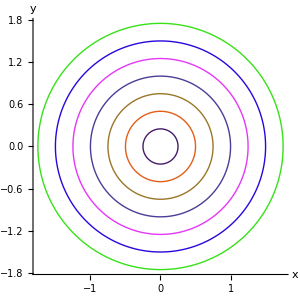
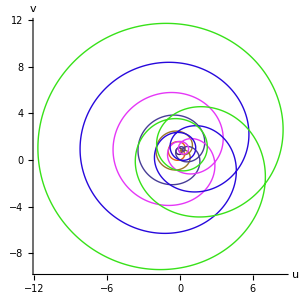

```mathematica
expr=(z+1)(z-.5)(z-1.5I);
pts=makeCirclePoints[.25,1.75,.25];
circleColors=makeRandomColors[pts]
n=2;
m=3;
makeImage[pts,expr,n,m,circleColors]
```

### makeGridPoints will make a grid of lines given user entered parameters

```mathematica
Clear[fSpace,makeVerticalPts,makeHorizontalPts,makeGridPts,makeLogVerticalPts,makeLogHorizontalPts,makeLogVerticalPts2,makeLogHorizontalPts2]
```

```mathematica
fSpace[min_,max_,steps_,f_: Log]:=Module[{},N[InverseFunction[f]/@Range[f@min,f@max,(f@max-f@min)/(steps-1)]]]
```

```mathematica
makeVerticalPts[min_,max_,ptsPerLine_,numLines_]:=Module[{horiPts},
horiPts=Table[Table[{x,y},{y,Range[min,max,(max-min)/(ptsPerLine-1)]}],{x,min,max,(max-min)/(numLines-1)}];
Return[horiPts]
]

makeHorizontalPts[min_,max_,ptsPerLine_,numLines_]:=Module[{horiPts},
horiPts=Table[Table[{x,y},{x,Range[min,max,(max-min)/(ptsPerLine-1)]}],{y,min,max,(max-min)/(numLines-1)}];
Return[horiPts]
]

makeGridPts[min_,max_,ptsPerLine_,numLines_]:=Module[{vertPts,horiPts,pts},
vertPts=makeVerticalPts[min,max,ptsPerLine,numLines];
horiPts=makeHorizontalPts[min,max,ptsPerLine,numLines];
pts=Join[horiPts,vertPts];
Return[pts]
]

makeLogVerticalPts2[min_,max_,ptsPerLine_,numLines_]:=Module[{vertPts},
vertPts=Table[Table[{x,y},{y,fSpace[min,max,ptsPerLine]}],{x,min,max,(max-min)/(numLines-1)}];
Return[Re[vertPts]]
]

makeLogHorizontalPts2[min_,max_,ptsPerLine_,numLines_]:=Module[{horiPts},
horiPts=Table[Table[{x,y},{x,fSpace[min,max,ptsPerLine]}],{y,min,max,(max-min)/(numLines-1)}];
Return[Re[horiPts]]
]

makeLogGridPts[min_,max_,ptsPerLine_,numLines_]:=Module[{vertLogPts,horiLogPts,pts},
vertLogPts=makeLogVerticalPts[min,max,ptsPerLine,numLines];
horiLogPts=makeLogHorizontalPts[min,max,ptsPerLine,numLines];
pts=Join[horiLogPts,vertLogPts];
Return[pts]
]

makeLogVerticalPts[min_,max_,ptsPerLine_,numLines_]:=Module[{posVertPts,negVertPts},
posVertPts=Table[Table[{x,y},{y,fSpace[.001,max,Floor[ptsPerLine/2]]}],{x,min,max,(max-min)/(numLines-1)}];
negVertPts=Table[Table[{x,y},{y,fSpace[min,-.001,Floor[ptsPerLine/2]]}],{x,min,max,(max-min)/(numLines-1)}];
pts=MapThread[Join,{negVertPts,posVertPts}];
Return[Re[pts]]
]

makeLogHorizontalPts[min_,max_,ptsPerLine_,numLines_]:=Module[{posHoriPts,negHoriPts},
posHoriPts=Table[Table[{x,y},{x,fSpace[.01,max,Floor[ptsPerLine/2]]}],{y,min,max,(max-min)/(numLines-1)}];
negHoriPts=Table[Table[{x,y},{x,fSpace[min,-.01,Floor[ptsPerLine/2]]}],{y,min,max,(max-min)/(numLines-1)}];
pts=MapThread[Join,{negHoriPts,posHoriPts}];
Return[Re[pts]]
]
```

### old

```mathematica
makeVerticalPts[start_,end_,stepSize_,lineSpacing_]:=Module[{vertPts},
newStep=stepSize+RandomReal[{.01,.02}];
vertPts=Table[Table[{x,y},{y,start,end,newStep}],{x,start,end,lineSpacing}];
Return[vertPts]
]

makeHorizontalPts[start_,end_,stepSize_,lineSpacing_]:=Module[{horiPts},
newStep=stepSize+RandomReal[{.01,.02}];
horiPts=Table[Table[{x,y},{x,start,end,newStep}],{y,start,end,lineSpacing}];
Return[horiPts]
]
```

```mathematica
makeRandomColors[pts_]:=Module[{colors},
colors=RandomColor[Length[pts]];
Return[colors]]
```

### Equal space test constants

```mathematica
numPts=1000;
numLines=3;
min=-10;
max=10;
expr=z^3
```

z^3

#### first make vertical lines

{7,1,2}

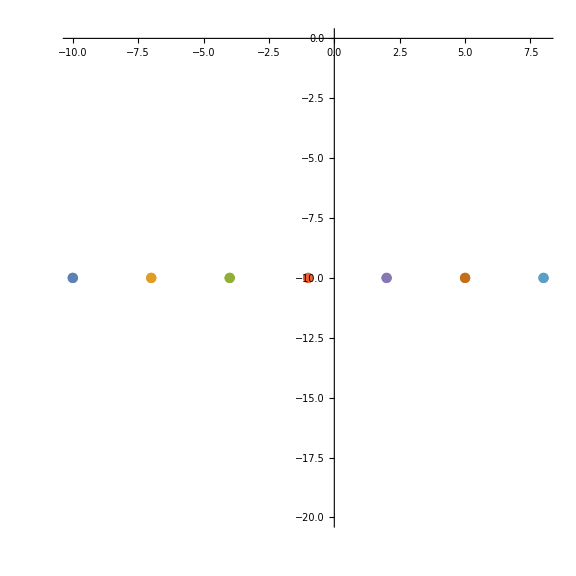

```mathematica
vertPts=makeVerticalPts[min,max,numPts,numLines];
Dimensions[vertPts]
ListPlot[vertPts,ImageSize->Large,AspectRatio->1]
```

#### second horizontal lines

{7,1,2}

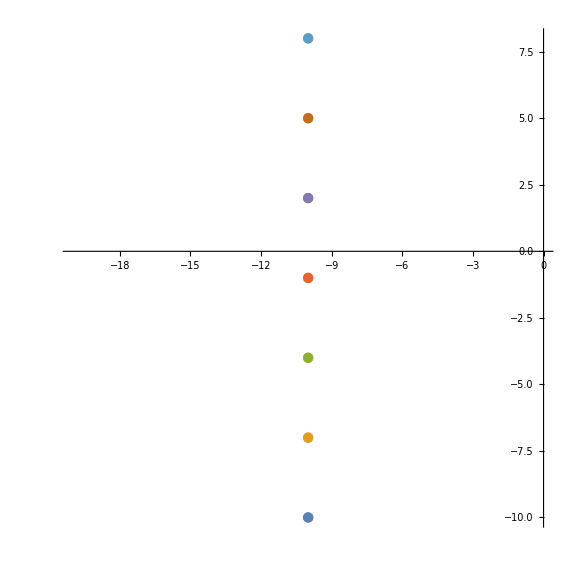

```mathematica
horiPts=makeHorizontalPts[min,max,numPts,numLines];
Dimensions[horiPts]
ListPlot[horiPts,ImageSize->Large,AspectRatio->1]
```

### Log test constants

```mathematica
ptsPerLine=100;
numLines=3;
min=-100;
max=100;
expr=z^3
```

z^3

{3,100,2}

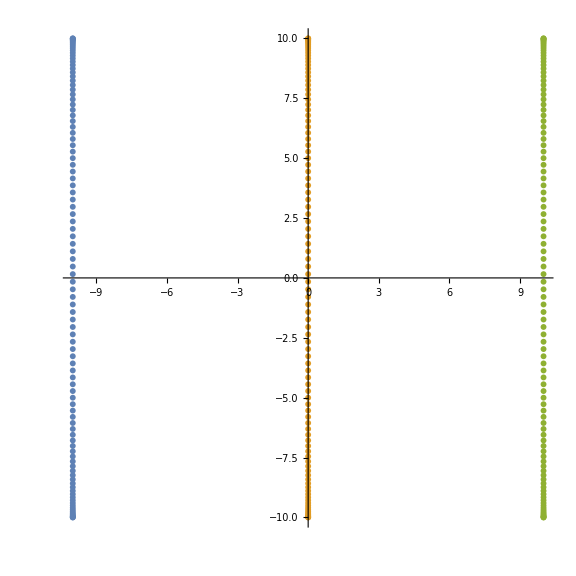

```mathematica
logVertPts=makeLogVerticalPts2[-10,10,ptsPerLine,numLines];
Dimensions[logVertPts]
ListPlot[logVertPts,ImageSize->Large,AspectRatio->1]
```

```mathematica
Range[-10,10,20/(21-1)]
```

{-10,-9,-8,-7,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10}

```mathematica
Log[0]
```

-∞

```mathematica
N@Re@Log[Range[-3,3,1/10]]
```

{1.09861,1.06471,1.02962,0.993252,0.955511,0.916291,0.875469,0.832909,0.788457,0.741937,0.693147,0.641854,0.587787,0.530628,0.470004,0.405465,0.336472,0.262364,0.182322,0.0953102,0.,-0.105361,-0.223144,-0.356675,-0.510826,-0.693147,-0.916291,-1.20397,-1.60944,-2.30259,-∞,-2.30259,-1.60944,-1.20397,-0.916291,-0.693147,-0.510826,-0.356675,-0.223144,-0.105361,0.,0.0953102,0.182322,0.262364,0.336472,0.405465,0.470004,0.530628,0.587787,0.641854,0.693147,0.741937,0.788457,0.832909,0.875469,0.916291,0.955511,0.993252,1.02962,1.06471,1.09861}

#### first make vertical lines

{3,100,2}

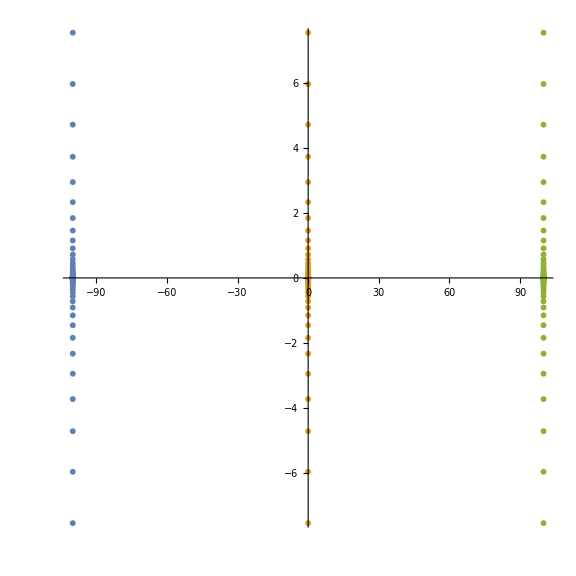

```mathematica
logVertPts=makeLogVerticalPts[min,max,ptsPerLine,numLines];
Dimensions[logVertPts]
ListPlot[logVertPts,ImageSize->Large,AspectRatio->1]
```

#### second horizontal lines

{3,100,2}

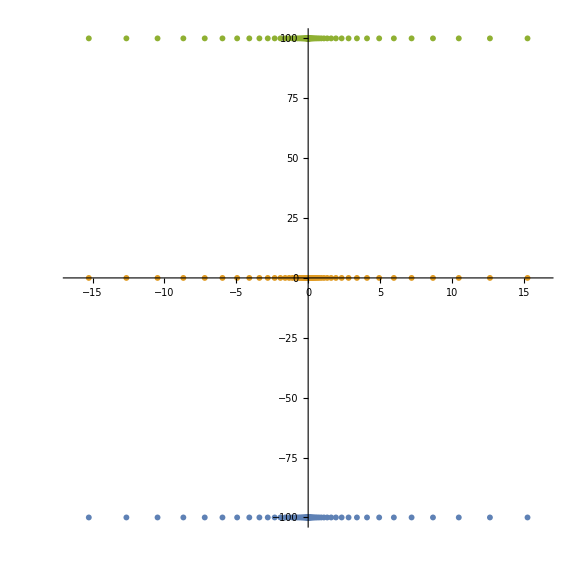

```mathematica
logHoriPts=makeLogHorizontalPts[min,max,ptsPerLine,numLines];
Dimensions[logHoriPts]
ListPlot[logHoriPts,ImageSize->Large,AspectRatio->1]
```

### Next try to make a grid

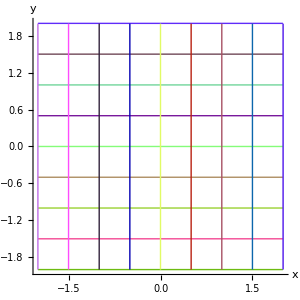
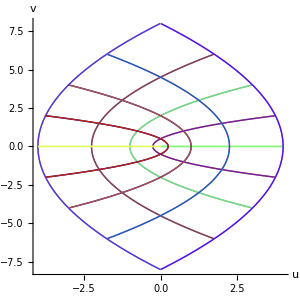

```mathematica
gridPts=makeGridPts[-2,2,.005,.5];
gridColors=makeRandomColors[gridPts];
makeImage[gridPts,z^2,Automatic,10,gridColors]
```

## Experiment with Riemann sphere stereographic projection

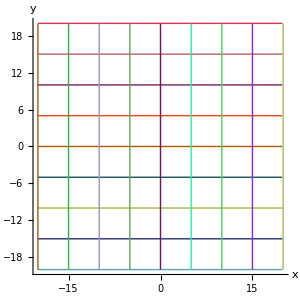
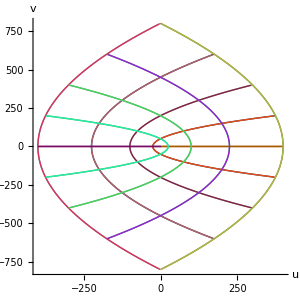

```mathematica
gridPts=makeGridPts[-20,20,.1,5];
gridColors=makeRandomColors[gridPts];
makeImage[gridPts,z^2,Automatic,10,gridColors]
```

```mathematica
gridPts[[1]][[1]]
```

{-20.,-20}

```mathematica
complexTo3D[point_]:=Module[{x,y,z,mix,X,Y,Z},
x=point[[1]];
y=point[[2]];
mix=(2x+ⅈ 2y)/(1+x^2+y^2);
X=Re[mix];
Y=Im[mix];
z=x+ⅈ y;
Z=(Abs[z]^2-1)/(Abs[z]^2+1);
Return[{X,Y,Z}]
]

complexPtsTo3D[points_]:=Module[{spherePts3D},
spherePts3D=complexTo3D[#]&/@#&/@points;
Return[spherePts3D]
]
```

```mathematica
complexTo3D[{1,1}]
```

{2/3,2/3,1/3}

```mathematica
pts3D=complexTo3D[#]&/@#&/@gridPts;
colors3D=makeRandomColors[pts3D]
```

{RGBColor[0.7142101052155962, 0.2655068395519167, 0.9531021637736445],RGBColor[0.8861334320404295, 0.33771212172069287, 0.35059261744410875],RGBColor[0.8494813631214149, 0.7716203370132753, 0.33478797293735996],RGBColor[0.13452646086247988, 0.655007222019806, 0.18767195080073207],RGBColor[0.9339771428431376, 0.14120875474317085, 0.5358074234041084],RGBColor[0.059649418610490335, 0.010150782068906405, 0.7902725024240309],RGBColor[0.39606935659438447, 0.5646179884327582, 0.25109606915248706],RGBColor[0.28933242038699003, 0.09113035682035986, 0.9199703906959735],RGBColor[0.8808798788270282, 0.34392386696473887, 0.42989838729564345],RGBColor[0.2917958213086995, 0.9749224975920787, 0.8385446400956036],RGBColor[0.6146228293546501, 0.51415983153688, 0.4588495033198532],RGBColor[0.7284313501513968, 0.5736781194585607, 0.3998159135357866],RGBColor[0.04063656836577767, 0.37030762656403593, 0.6118399378406252],RGBColor[0.11367802495433166, 0.3327201657310612, 0.6164948164249067],RGBColor[0.6167984949040826, 0.044260097514120744, 0.9995634383312744],RGBColor[0.8913024516836987, 0.3609095453833684, 0.8626145969326426],RGBColor[0.06831888794483998, 0.17129110728691255, 0.8633056938022794],RGBColor[0.3761098121042319, 0.7501226580213458, 0.3515292696808565]}

```mathematica
ListPointPlot3D[pts3D,PlotRange->All,AspectRatio->1,ImageSize->Large]
```

-Graphics3D-

```mathematica
Graphics3D[MapThread[{#1,Thick,Line[#2]}&,{colors3D,pts3D}]]
```

-Graphics3D-

### 1 to 100 log spaced

```mathematica
Re@fSpace[-20,20,100]
```

{-20.,-19.9899,-19.9597,-19.9094,-19.8391,-19.7488,-19.6386,-19.5086,-19.359,-19.1899,-19.0014,-18.7939,-18.5674,-18.3222,-18.0585,-17.7767,-17.477,-17.1597,-16.8251,-16.4735,-16.1054,-15.7211,-15.3209,-14.9053,-14.4747,-14.0295,-13.5702,-13.0972,-12.6111,-12.1122,-11.6011,-11.0784,-10.5445,-10.,-9.44542,-8.88133,-8.3083,-7.7269,-7.13772,-6.54136,-5.93841,-5.32948,-4.71518,-4.09613,-3.47296,-2.8463,-2.21676,-1.585,-0.951638,-0.317319,0.317319,0.951638,1.585,2.21676,2.8463,3.47296,4.09613,4.71518,5.32948,5.93841,6.54136,7.13772,7.7269,8.3083,8.88133,9.44542,10.,10.5445,11.0784,11.6011,12.1122,12.6111,13.0972,13.5702,14.0295,14.4747,14.9053,15.3209,15.7211,16.1054,16.4735,16.8251,17.1597,17.477,17.7767,18.0585,18.3222,18.5674,18.7939,19.0014,19.1899,19.359,19.5086,19.6386,19.7488,19.8391,19.9094,19.9597,19.9899,20.}

```mathematica
Range[-1,1,(1-(-1))/(20-1)]
```

{-1,-17/19,-15/19,-13/19,-11/19,-9/19,-7/19,-5/19,-3/19,-1/19,1/19,3/19,5/19,7/19,9/19,11/19,13/19,15/19,17/19,1}

## Log grid Riemann sphere

```mathematica
ptsPerLine=100;
numLines=5;
min=-10000;
max=10000;
expr=z^3
```

z^3

```mathematica
logGridPts=makeLogGridPts[min,max,ptsPerLine,numLines];
Dimensions[logGridPts]
```

{10,100,2}

```mathematica
logPts3D=pts3D=complexTo3D[#]&/@#&/@logGridPts;
Dimensions[logPts3D]
```

{10,100,3}

```mathematica
colors3D=makeRandomColors[logPts3D]
```

{RGBColor[0.23124764746645488, 0.5181856075590441, 0.0023855757836597213],RGBColor[0.8886162415866652, 0.3172385851365729, 0.8816320967121252],RGBColor[0.8016857804829489, 0.6941038701801332, 0.6133325061202031],RGBColor[0.829759386289326, 0.02412434375811756, 0.18279792432144815],RGBColor[0.8642629647139133, 0.8267870427942747, 0.8724095910040508],RGBColor[0.960659344537423, 0.9580835614463841, 0.09947359654283461],RGBColor[0.33013663823057593, 0.9256134931737465, 0.38603228856926686],RGBColor[0.646337578849197, 0.5931111477000615, 0.7398710815537066],RGBColor[0.08523675872264214, 0.48140208806933416, 0.48065610469084863],RGBColor[0.6173402580742329, 0.34638245868839523, 0.5734733734023123]}

```mathematica
ListPointPlot3D[logPts3D,PlotRange->All,AspectRatio->1,ImageSize->Large]
```

-Graphics3D-

```mathematica
Graphics3D[MapThread[{#1,Thick,Line[#2]}&,{colors3D,pts3D}]]
```

-Graphics3D-

## Trying to get circular spaced points

```mathematica
Clear[makeRiemannUnitCirclePts]
```

```mathematica
makeRiemannUnitCirclePts[numPts_]:=Module[
{angles, pts},
angles=N@Range[0Pi,2Pi,(2 Pi - 0Pi)/(numPts - 1)];
pts=Table[{Cos[ang],0,Sin[ang]},{ang,angles}];
Return[pts]
]
```

```mathematica
riemannPointToComplexPlane[{X_,Y_,Z_}]:=Module[{sol,pair},
sol=Solve[{x+ⅈ y==(X+ⅈ Y)/(1-Z)},{x∈Reals,y∈Reals}];
pair=({x,y}/.sol)[[1]];
Return[pair]
]
```

```mathematica
makeSphereSpacedPoints[numPts_]:=Module[{pts,complexPts,realPts},
pts=makeRiemannUnitCirclePts[numPts];
complexPts=riemannPointToComplexPlane[#]&/@pts;
realPts=complexPts[[All,1]];
Return[realPts]
]
```

{1.,1.40059,2.04553,3.35894,8.02247,-24.1778,-4.76922,-2.56278,-1.67822,-1.1807,-0.846957,-0.595871,-0.390201,-0.209678,-0.0413603,0.12465,0.297713,0.48887,0.713986,1.}

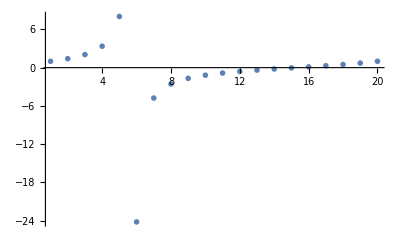

```mathematica
sphericalPts=makeSphereSpacedPoints[20]
ListPlot[sphericalPts,PlotStyle->PointSize[.01],PlotRange->All]
```

```mathematica
makeSphereSpacedPoints[20]
```

{1.,1.40059,2.04553,3.35894,8.02247,-24.1778,-4.76922,-2.56278,-1.67822,-1.1807,-0.846957,-0.595871,-0.390201,-0.209678,-0.0413603,0.12465,0.297713,0.48887,0.713986,1.}

```mathematica
horiPts=Table[Table[{x,y},{x,{1.,1.4005871438998048,2.045532694709038,3.3589407898715407,8.022471262465187,-24.177770864938736,-4.769218689284606,-2.5627803610641804,-1.67821653689189,-1.1806977689241733,-0.8469567964977006,-0.5958706627048448,-0.3902012108383555,-0.20967795044642917,-0.04136030594326412,0.12464987000685275,0.2977128989636771,0.4888702109658738,0.7139862766522278,0.9999999999999998}}],{y,-1,1,(1-(-1))/(2-1)}]
```

{{{1.,-1},{1.40059,-1},{2.04553,-1},{3.35894,-1},{8.02247,-1},{-24.1778,-1},{-4.76922,-1},{-2.56278,-1},{-1.67822,-1},{-1.1807,-1},{-0.846957,-1},{-0.595871,-1},{-0.390201,-1},{-0.209678,-1},{-0.0413603,-1},{0.12465,-1},{0.297713,-1},{0.48887,-1},{0.713986,-1},{1.,-1}},{{1.,1},{1.40059,1},{2.04553,1},{3.35894,1},{8.02247,1},{-24.1778,1},{-4.76922,1},{-2.56278,1},{-1.67822,1},{-1.1807,1},{-0.846957,1},{-0.595871,1},{-0.390201,1},{-0.209678,1},{-0.0413603,1},{0.12465,1},{0.297713,1},{0.48887,1},{0.713986,1},{1.,1}}}

```mathematica
Clear[makeHorizontalLines]
```

```mathematica
makeHorizontalLines[min_,max_,ptsPerLine_,numLines_]:=Module[{horiPts,spherePts},
spherePts=makeSphereSpacedPoints[ptsPerLine];
horiPts=Table[Table[{x,y},{x,spherePts}],{y,min,max,(max-min)/(numLines-1)}];
Return[horiPts]
]
makeVerticalLines[min_,max_,ptsPerLine_,numLines_]:=Module[{horiPts,spherePts},
spherePts=makeSphereSpacedPoints[ptsPerLine];
horiPts=Table[Table[{x,y},{y,spherePts}],{x,min,max,(max-min)/(numLines-1)}];
Return[horiPts]
]
makeGrid[min_,max_,ptsPerLine_,numLines_]:=Module[{vertPts,horiPts,pts},
vertPts=makeHorizontalLines[min,max,ptsPerLine,numLines];
horiPts=makeVerticalLines[min,max,ptsPerLine,numLines];
pts=Join[horiPts,vertPts];
Return[pts]
]
```

```mathematica
min=-3;
max=3;
ptsPerLine=200;
numLines=3;
```

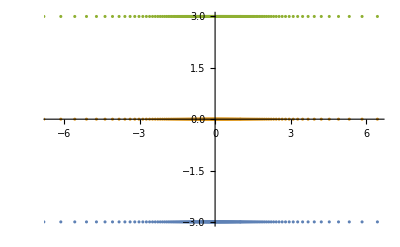

```mathematica
horiPts=makeHorizontalLines[min,max,ptsPerLine,numLines];
ListPlot[horiPts]
```

```mathematica
horiPts//Dimensions
```

{3,200,2}

```mathematica
expr=1/z;
image={Re[expr /. z -> #[[1]] + ⅈ #[[2]]], Im[expr /. z -> #[[1]] + ⅈ #[[2]]]}&/@#&/@horiPts;
Dimensions[image]
```

{3,200,2}

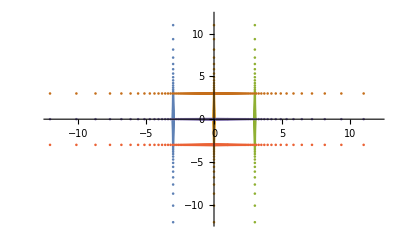

```mathematica
gridPts=makeGrid[min,max,ptsPerLine,numLines];
ListPlot[gridPts]
```

```mathematica
spherePts3D=complexTo3D[#]&/@#&/@gridPts;
colors2=makeRandomColors[spherePts3D]
```

{RGBColor[0.6239545598400853, 0.9714825580552091, 0.9680219516015531],RGBColor[0.7672460841088613, 0.3907048360247405, 0.7883650726813975],RGBColor[0.6870658802592007, 0.36882947356111684, 0.4722467689551342],RGBColor[0.3574632439868981, 0.8854442670495681, 0.3036019689527516],RGBColor[0.03172356668364018, 0.16863603499374014, 0.9464899496643764],RGBColor[0.8755865527107782, 0.26442454930540804, 0.7141027443838255]}

```mathematica
ListPointPlot3D[spherePts3D,PlotRange->Full,AspectRatio->1,ImageSize->Large]
```

-Graphics3D-

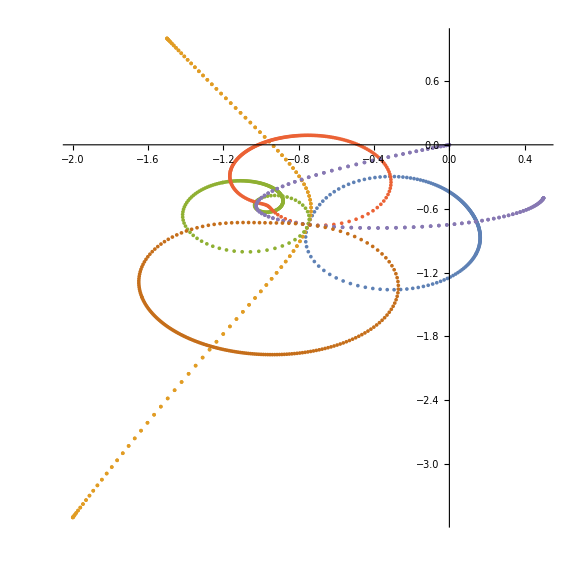

```mathematica
expr=(z-1)(z+1.5)(z+.5+I.5);
image={Re[expr /. z -> #[[1]] + ⅈ #[[2]]], Im[expr /. z -> #[[1]] + ⅈ #[[2]]]}&/@#&/@spherePts3D;
ListPlot[image,PlotRange->Full,ImageSize->Large,AspectRatio->1]
```

```mathematica
Graphics3D[cylinders[complexPtsTo3D[image],.01]]
```

-Graphics3D-

```mathematica
takingPts[takes_,pts_]:=Module[{newPts},
newPts=Take[pts,#]&/@takes;
Return[newPts]]

cylinderPts[pts_]:=Module[{takes,returnPts},
takes=Table[{x,x+1},{x,1,Dimensions[pts][[2]]-1}];
returnPts=takingPts[takes,#]&/@pts
]

cylinders[pts_,radius_]:=Module[{},
Return[Cylinder[#,radius]&/@#&/@cylinderPts[pts]]]
```

```mathematica
Export["grid.stl",Graphics3D[cylinders[spherePts3D,.01],{"STL,","BinaryFormat"->True}]]
```

grid.stl

```mathematica
Import["grid.stl"]
```

-Graphics3D-

```mathematica
Export["grid_10_7.stl",Graphics3D[cylinders[complexPtsTo3D[makeGrid[-3,3,100,12]],.01]],{"STL,","BinaryFormat"->True}]
```

grid_10_7.stl

```mathematica
grid107=Import["grid_10_7.stl"]
```

-Graphics3D-